```mathematica
G1[x_] := AA (Exp[- I k x] - Exp[I k x])
G2[x_] := CC Exp[-I k x] + DD Exp[I k x]
G3[x_] := Exp[- I k x] + EE Exp[I k x]
```

```mathematica
Solve[{
G1[ss] == G2[ss],
G2[aa] == G3[aa],
G2'[ss] - G1'[ss] == 1,
G3'[aa] - G2'[aa] == uu * G2[aa]}, {AA, CC, DD, EE}]
```

{{AA→-(ⅇ^(-ⅈ k ss) (2 ⅇ^(2 ⅈ k ss) k+4 ⅈ ⅇ^(ⅈ k ss) k^2-ⅈ ⅇ^(2 ⅈ aa k) uu+ⅈ ⅇ^(2 ⅈ k ss) uu))/(2 k (-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu)),CC→(ⅇ^(-ⅈ k ss) (4 ⅇ^(ⅈ k ss) k^2-ⅇ^(2 ⅈ aa k) uu+ⅇ^(2 ⅈ aa k+2 ⅈ k ss) uu))/(2 k (2 k+ⅈ uu-ⅈ ⅇ^(2 ⅈ aa k) uu)),DD→-(ⅈ ⅇ^(-ⅈ k ss))/(2 k)+(ⅇ^(-ⅈ k ss) (2 ⅇ^(2 ⅈ k ss) k+4 ⅈ ⅇ^(ⅈ k ss) k^2-ⅈ ⅇ^(2 ⅈ aa k) uu+ⅈ ⅇ^(2 ⅈ k ss) uu))/(2 k (-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu)),EE→-(ⅇ^(-2 ⅈ aa k-ⅈ k ss) (-ⅇ^(2 ⅈ aa k)+ⅇ^(2 ⅈ aa k+2 ⅈ k ss)+2 ⅈ ⅇ^(2 ⅈ aa k+ⅈ k ss) k-ⅇ^(ⅈ k ss) uu+ⅇ^(2 ⅈ aa k+ⅈ k ss) uu))/(2 ⅈ k-uu+ⅇ^(2 ⅈ aa k) uu)}}

```mathematica
AA := -(ⅇ^(-ⅈ k ss) (2 ⅇ^(2 ⅈ k ss) k+4 ⅈ ⅇ^(ⅈ k ss) k^2-ⅈ ⅇ^(2 ⅈ aa k) uu+ⅈ ⅇ^(2 ⅈ k ss) uu))/(2 k (-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu))
```

```mathematica
CC := (ⅇ^(-ⅈ k ss) (4 ⅇ^(ⅈ k ss) k^2-ⅇ^(2 ⅈ aa k) uu+ⅇ^(2 ⅈ aa k+2 ⅈ k ss) uu))/(2 k (2 k+ⅈ uu-ⅈ ⅇ^(2 ⅈ aa k) uu))
```

```mathematica
DD := -(ⅈ ⅇ^(-ⅈ k ss))/(2 k)+(ⅇ^(-ⅈ k ss) (2 ⅇ^(2 ⅈ k ss) k+4 ⅈ ⅇ^(ⅈ k ss) k^2-ⅈ ⅇ^(2 ⅈ aa k) uu+ⅈ ⅇ^(2 ⅈ k ss) uu))/(2 k (-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu))
```

```mathematica
EE := -(ⅇ^(-2 ⅈ aa k-ⅈ k ss) (-ⅇ^(2 ⅈ aa k)+ⅇ^(2 ⅈ aa k+2 ⅈ k ss)+2 ⅈ ⅇ^(2 ⅈ aa k+ⅈ k ss) k-ⅇ^(ⅈ k ss) uu+ⅇ^(2 ⅈ aa k+ⅈ k ss) uu))/(2 ⅈ k-uu+ⅇ^(2 ⅈ aa k) uu)
```

```mathematica
G4[x_] := AAA (Exp[- I k x] - Exp[I k x])
```

```mathematica
G5[x_] := CCC Exp[-I k x] + DDD Exp[I k x]
```

```mathematica
G6[x_] := Exp[-I k x] + EEE Exp[I k x]
```

```mathematica
Solve[{
G4[aa] == G5[aa],
G5'[aa] - G4'[aa] == uu * G4[aa],
G5[ss] == G6[ss],
G6'[ss] - G5'[ss] == 1}, {AAA, CCC, DDD, EEE}]
```

{{AAA→-(ⅇ^(ⅈ k ss)+2 ⅈ k)/(-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu),CCC→-(ⅈ (ⅇ^(ⅈ k ss)+2 ⅈ k))/(2 k),DDD→-(ⅇ^(-2 ⅈ aa k) (-ⅈ ⅇ^(ⅈ k ss)+2 k) (2 ⅈ ⅇ^(2 ⅈ aa k) k-uu+ⅇ^(2 ⅈ aa k) uu))/(2 k (2 ⅈ k-uu+ⅇ^(2 ⅈ aa k) uu)),EEE→-ⅇ^(-2 ⅈ k ss)+(ⅈ (ⅇ^(-2 ⅈ aa k)-ⅇ^(-2 ⅈ k ss)) (ⅇ^(ⅈ k ss)+2 ⅈ k))/(2 k)+((1-ⅇ^(-2 ⅈ aa k)) (ⅇ^(ⅈ k ss)+2 ⅈ k))/(-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu)}}

```mathematica
AAA := -(ⅇ^(ⅈ k ss)+2 ⅈ k)/(-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu)
CCC:= -(ⅈ (ⅇ^(ⅈ k ss)+2 ⅈ k))/(2 k)
DDD := -(ⅇ^(-2 ⅈ aa k) (-ⅈ ⅇ^(ⅈ k ss)+2 k) (2 ⅈ ⅇ^(2 ⅈ aa k) k-uu+ⅇ^(2 ⅈ aa k) uu))/(2 k (2 ⅈ k-uu+ⅇ^(2 ⅈ aa k) uu))
EEE := -ⅇ^(-2 ⅈ k ss)+(ⅈ (ⅇ^(-2 ⅈ aa k)-ⅇ^(-2 ⅈ k ss)) (ⅇ^(ⅈ k ss)+2 ⅈ k))/(2 k)+((1-ⅇ^(-2 ⅈ aa k)) (ⅇ^(ⅈ k ss)+2 ⅈ k))/(-2 ⅈ k+uu-ⅇ^(2 ⅈ aa k) uu)
```

```mathematica
GG1[x_, s_] := If[x < s, G1[x], If[x < aa, G2[x], G3[x]]] /. {ss -> s}
GG2[x_, s_] := If[x < s, If[x < aa, G4[x], G5[x]], G6[x]] /. {ss -> s}
```

```mathematica
GG[x_, s_] := If[s < aa, GG1[x, s], GG2[x, s]]
```

```mathematica
uu := 1
```

```mathematica
aa := 1
```

```mathematica
TransferFunctionPoles[TransferFunctionModel[GG[0.5, 0.6],k ]]
```

{{{0,ConditionalExpression[(0.-0.5 ⅈ)+(0.+0.5 ⅈ) ProductLog[C[1],ⅇ],C[1]∈Integers]}}}

```mathematica
0.5 I * N[ProductLog[-3, E]]
```

8.58575-0.924507 ⅈ

```mathematica
AAA := (2 ⅇ^(-ⅈ aa k) k)/(ⅈ k Cos[aa k]+k Sin[aa k]+ⅈ uu Sin[aa k])
```

```mathematica
pf[x_] := Norm[AAA Sin[k x]]^2
```

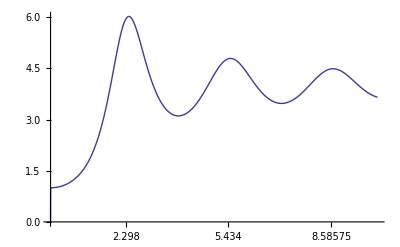

```mathematica
Plot[FindMaxValue[pf[x],{x,aa / 2}], {k, 0.0, 10.0}, Ticks->{{2.298, 5.434, 8.58575},Automatic}]
```

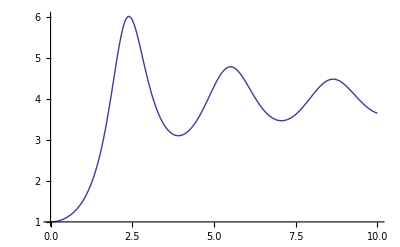

```mathematica
Plot[Norm[AAA]^2, {k, 0.0, 10.0}]
```

```mathematica
Re[GG[0.5, 0.6]] /. {k -> 1 + 50.2 I}
```

6.91402×10^10

```mathematica
DensityPlot[Re[GG[0.5, 0.6]] /. {k -> x + I y}, {x, -100.0, 100.0}, {y, -100.0, 100.0},PlotPoints->100, AxesLabel->Automatic]
```

-Graphics-